```mathematica
data0=Import[NotebookDirectory[]<>"mixmu.dat"];
dataold=Import[NotebookDirectory[]<>"mixmu-old.dat"];
```

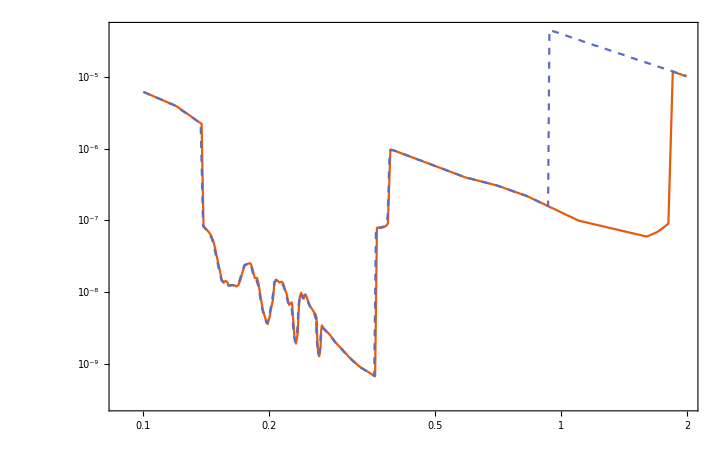

```mathematica
ListLogLogPlot[{data0,dataold},PlotTheme->"Scientific",Joined->True,PlotStyle->{Automatic,Dashed},PlotRange->{Automatic,Automatic}]
```